```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
α=2/3;β=4/3;γ=1;δ=1;
sols=NDSolve[{x'[t]==α x[t] - β x[t] y[t],y'[t]==δ x[t] y[t] - γ y[t],x[0]==0.9,y[0]==0.9},{x,y},{t,0,100}]
```

{{x→InterpolatingFunction[…],y→InterpolatingFunction[…]}}

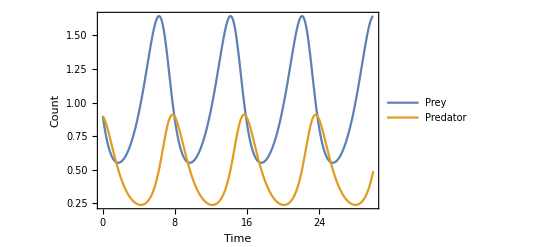

```mathematica
g=Plot[Evaluate[{x[t],y[t]}/.sols],{t,0,30},Frame->{True,True,False,False},FrameLabel->{"Time","Count"},LabelStyle->{Black,FontSize->14},PlotLegends->{"Prey", "Predator"}]
```

```mathematica
Export["../documents/figures/lotka-volterra.pdf",g]
```

../documents/figures/lotka-volterra.pdf

```mathematica
prey[t_]:=Evaluate[x[t]/.sols][[1]]
```

```mathematica
ts=Table[t,{t,0,30,10}];
rands=RandomVariate[NormalDistribution[0, 0.3],Length@ts];
obs = Table[{ts[[i]],prey[ts[[i]]]+rands[[i]]},{i,1,Length@ts}];
```

```mathematica
obs
```

{{0,1.14885},{10,0.657148},{20,0.8278},{30,1.41799}}

```mathematica
col1=ColorData[97,"ColorList"][[1]];
cols={col1,Darker[Red],Darker[Green],Magenta};
imagesize=400;
```

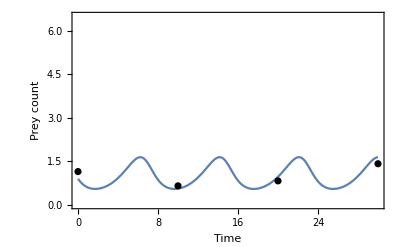

```mathematica
{β1,γ1}={β,γ};
g1=Show[Plot[Evaluate[{x[t]}/.sols],{t,0,30},PlotRange->{Automatic,{0,6.5}},Frame->{True,True,False,False},FrameLabel->{"Time","Prey count"},LabelStyle->{Black,FontSize->14}],ListPlot[obs,PlotStyle->Black],ImageSize->imagesize]
```

```mathematica
Export["../documents/figures/lotka-volterra-infer-1.pdf",g1]
```

../documents/figures/lotka-volterra-infer-1.pdf

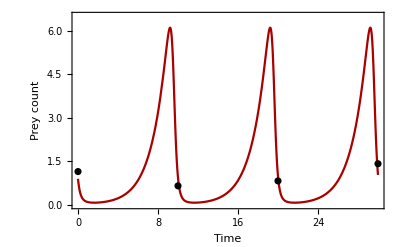

```mathematica
α=2/3;β=5;γ=1.38;δ=1;
{β2,γ2}={β,γ};
sols1=NDSolve[{x'[t]==α x[t] - β x[t] y[t],y'[t]==δ x[t] y[t] - γ y[t],x[0]==0.9,y[0]==0.9},{x,y},{t,0,100}];
g2=Show[Plot[Evaluate[{x[t]}/.sols1],{t,0,30},PlotRange->{Automatic,{0,6.5}},Frame->{True,True,False,False},FrameLabel->{"Time","Prey count"},LabelStyle->{Black,FontSize->14},PlotStyle->Darker[Red]],ListPlot[obs,PlotStyle->Black],ImageSize->imagesize]
```

```mathematica
Export["../documents/figures/lotka-volterra-infer-2.pdf",g2]
```

../documents/figures/lotka-volterra-infer-2.pdf

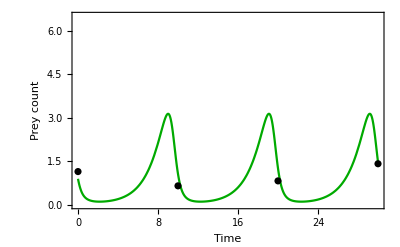

```mathematica
α=2/3;β=3;γ=0.91;δ=1;
{β3,γ3}={β,γ};
sols1=NDSolve[{x'[t]==α x[t] - β x[t] y[t],y'[t]==δ x[t] y[t] - γ y[t],x[0]==0.9,y[0]==0.9},{x,y},{t,0,100}];
g3=Show[Plot[Evaluate[{x[t]}/.sols1],{t,0,30},PlotRange->{Automatic,{0,6.5}},Frame->{True,True,False,False},FrameLabel->{"Time","Prey count"},LabelStyle->{Black,FontSize->14},PlotStyle->Darker[Green]],ListPlot[obs,PlotStyle->Black],ImageSize->imagesize]
```

```mathematica
Export["../documents/figures/lotka-volterra-infer-3.pdf",g3]
```

../documents/figures/lotka-volterra-infer-3.pdf

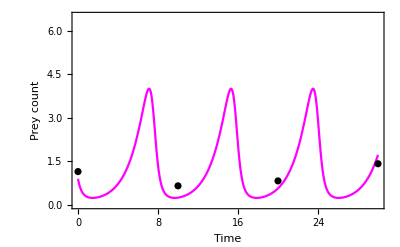

```mathematica
α=2/3;β=3;γ=1.34;δ=1;
{β4,γ4}={β,γ};
sols1=NDSolve[{x'[t]==α x[t] - β x[t] y[t],y'[t]==δ x[t] y[t] - γ y[t],x[0]==0.9,y[0]==0.9},{x,y},{t,0,100}];
g4=Show[Plot[Evaluate[{x[t]}/.sols1],{t,0,30},PlotRange->{Automatic,{0,6.5}},Frame->{True,True,False,False},FrameLabel->{"Time","Prey count"},LabelStyle->{Black,FontSize->14}, PlotStyle->Magenta],ListPlot[obs,PlotStyle->Black],ImageSize->imagesize]
```

```mathematica
Export["../documents/figures/lotka-volterra-infer-4.pdf",g4]
```

../documents/figures/lotka-volterra-infer-4.pdf

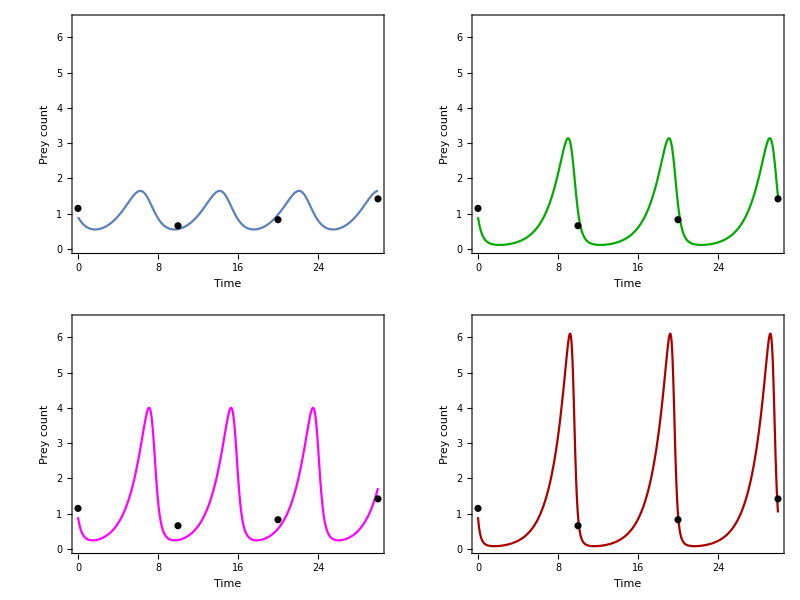

```mathematica
gFinal=Grid[{{g1,g3},{g4,g2}}]
```

```mathematica
Export["../documents/figures/lotka-volterra-inference-other.pdf",gFinal]
```

../documents/figures/lotka-volterra-inference-other.pdf

## Calculate distance

```mathematica
distance[alpha_,beta_?NumberQ,gamma_?NumberQ,delta_,obs__]:=Module[{sols1=NDSolve[{x'[t]==alpha x[t] - beta x[t] y[t],y'[t]==delta  x[t] y[t] - gamma y[t],x[0]==0.9,y[0]==0.9},{x,y},{t,0,100}][[1,1,2]],ts=obs[[All,1]],vals},vals=Flatten@Table[sols1[t],{t,ts}];Sqrt[Mean[(vals-obs[[All,2]])^2]]]
```

```mathematica
betas=Range[1,6,0.01];
gammas=Range[0.8,1.5,0.002];
combs=Tuples[{betas,gammas}];
dists={#1,#2,1/distance[α,#1,#2,δ,obs]}&@@@combs;
```

```mathematica
gBig=Show[ListDensityPlot[dists,ColorFunction->"SouthwestColors",PlotRange->{{1,6},Automatic,{0,7.7}},Frame->True,FrameLabel->{"β","γ"},LabelStyle->{Black,FontSize->18}],ListPlot[{{{β1,γ1}},{{β2,γ2}},{{β3,γ3}},{{β4,γ4}}},PlotStyle->cols,PlotMarkers->{"✶", Large}]]
```

-Graphics-

```mathematica
Export["../documents/figures/lotka-volterra-inference-big.png",gBig,ImageResolution->400]
```

../documents/figures/lotka-volterra-inference-big.png

## Local optimisation across surface

```mathematica
Clear[distance]
```

```mathematica
NMinimize[{distance[α,6,gamma,δ,obs],1.6>gamma>0.8},{gamma},Method->"NelderMead"]
```

{0.446617,{gamma→0.857661}}

```mathematica
pts=Reap[FindMinimum[{distance[α,beta,gamma,δ,obs],1.6>gamma>0.8&&1<beta<6},{{beta,5},{gamma,1.3}},StepMonitor:>Sow[{beta,gamma}]]][[2,1]];
```

```mathematica
Show[ListDensityPlot[dists,ColorFunction->"SouthwestColors",PlotRange->{{1,6},Automatic,{0,7.7}},Frame->True,FrameLabel->{"β","γ"},LabelStyle->{Black,FontSize->14}],ListPlot[pts,PlotStyle->Black,Joined->True,PlotMarkers->{Automatic, Medium},PlotRange->Full]]
```

-Graphics-